#### Problem 1

```mathematica
r[t_]:={ArcTan[t],2E^(2t),8t E^t}
r'[0]
```

{1,4,8}

```mathematica
rp[t_]:={t,E^t,t E^t}
Solve[(Integrate[rp[t],t]+{c1,c2,c3}/.{t->0})=={1,1,1},{c1,c2,c3}]
Integrate[rp[t],t]+{c1,c2,c3}/.%//Simplify//Flatten
```

{{c1→1,c2→0,c3→2}}

{1/2 (2+t^2),ⅇ^t,2+ⅇ^t (-1+t)}

#### Problem 2

```mathematica
r3[t_]:={2Cos[t],2Sin[t],√5 t}
ParametricPlot3D[r3[t],{t,0,5}]
```

-Graphics3D-

```mathematica
(* curvature k(t)=(|c'(t)×c''(t)|)/(|c'(t)|^3)*)
```

```mathematica
Assuming[t∈Reals,k[t_]=Norm[Cross[r3'[t],r3''[t]]]/Norm[r3'[t]]^3//Simplify]
```

2/9

```mathematica
F[t_]:={Cos[t],Sin[t],t/10}
```

```mathematica
ParametricPlot3D[{F[t],F[Pi]+F'[Pi](t-Pi),F[3Pi/4]+F'[3Pi/4](t-3Pi/4)},{t,0,10}]
```

-Graphics3D-

```mathematica
F[Pi]+F'[Pi](t-Pi)
```

{-1,π-t,π/10+1/10 (-π+t)}

```mathematica
n=Cross[F'[Pi],F'[3Pi/4]]//Simplify//Normalize
```

{(-2+√2)/(20 √(101/200+1/400 (2-√2)^2)),-1/(10 √(2 (101/200+1/400 (2-√2)^2))),-1/(√(2 (101/200+1/400 (2-√2)^2)))}

```mathematica
Dot[(F[Pi]-F[3Pi/4]),n]//Simplify//N
```

0.00427791

```mathematica
Dot[(F[Pi]-F[3Pi/4]),Cross[F'[Pi],F'[3Pi/4]]]//Simplify
```

1/80 (16-8 √2-√2 π)

```mathematica
ClearAll[n,k,a,x,y]
```

```mathematica
Solve[(m+k y)/(n - k)==x,k]
```

{{k→(-m+n x)/(x+y)}}

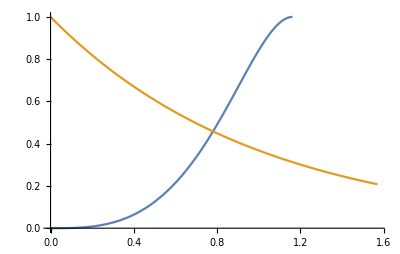

```mathematica
ParametricPlot[{{t^(1/3),Sin[t]},{t,E^(-t)}},{t,0,Pi/2}]
```

```mathematica
NSolve[Sin[t] == E^(-t^(1/3)), t,t∈Interval[0,Pi]]
```

NSolve::bdomv: Warning: t∈Interval[{0,0},{π,π}] is not a valid domain specification. Assuming it is a variable to eliminate.

NSolve::disj: Variable lists {t} and {t} should be disjoint.

NSolve[Sin[t]==ⅇ^(-t^(1/3)),t,t∈Interval[{0,0},{π,π}]]

```mathematica
ClearAll[t]
```

```mathematica
D[t^(1/3),t]
```

1/(3 t^(2/3))

```mathematica
r1[t_]:={t^(1/3),Sin[t]}
r2[t_]:={t,E^(-t)}
```

```mathematica
r1'[t]/.{t->0.780704}
```

{0.393147,0.710418}

```mathematica
r2'[t]/.{t->0.780704}
```

{1,-0.458083}

```mathematica
r1'[t]/.{t->1.425866}
```

{0.263123,0.144423}

```mathematica
r2'[t]/.{t->1.425866}
```

{1,-0.2403}

```mathematica
ArcCos[Dot[Normalize[{0.26312347920922063,0.14442348731194246}],Normalize[{1,-0.24030027303855833}]]]
```

0.737813

```mathematica
FindRootPlot
```

```mathematica
F[x_]:=Log[x]Exp[-x]
x2 = x1-F
```

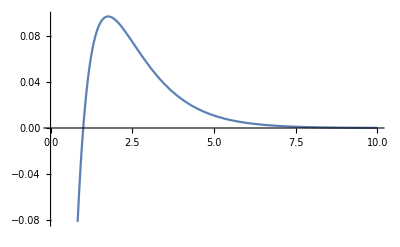

```mathematica
Plot[Log[x]Exp[-x],{x,0,10}]
```

```mathematica
FindRootPlot
```

```mathematica
NSolve[x^3-x-3==0,x]
```

{{x→-0.83585-1.04687 ⅈ},{x→-0.83585+1.04687 ⅈ},{x→1.6717}}

```mathematica
Series[x-(1-E^(-3x))/(9x E^(-3x)),{x,0,10}]
```

-1/3+x/2-x^2/2-(3 x^3)/8-(9 x^4)/40-(9 x^5)/80-(27 x^6)/560-(81 x^7)/4480-(27 x^8)/4480-(81 x^9)/44800-(243 x^10)/492800+O[x]^11

```mathematica
Sum[Sum[i-1+Sum[1,{k,1,j-1}],{j,1,i}],{i,1,n}]
```

1/2 (-1+n) n (1+n)

```mathematica
Sum[1+Sum[1,{j,k,n}],{k,1,n}]
```

1/2 (3 n+n^2)

```mathematica
ParametricPlot3D[{{-√2/4,-√2/2,1/2},{-√2/4,√2/2,1/2},{√3/2,0,√2/2}}.{1,0,0},{t,0,5}]
```

-Graphics3D-

```mathematica
Dot[{{-√2/4,-√2/2,1/2},{-√2/4,√2/2,1/2},{√3/2,0,√2/2}}.{1,0,0},{-√2/2,-√2/2,0}]
```

1/2

{-1/(2 √2),-1/(2 √2),(√3)/2}

```mathematica
Integrate
```

```mathematica
ClearAll[r]
```

```mathematica
A={{a,b},{r a,0}}
```

```mathematica
ReflectionMatrix
```

{{a,b},{a r,0}}

```mathematica
MatrixPower[A,n]//MatrixForm
```

((2^(-1-n) (-√a+√(a+4 b r)) (a-√a √(a+4 b r))^n)/(√(a+4 b r))-(2^(-1-n) (-√a-√(a+4 b r)) (a+√a √(a+4 b r))^n)/(√(a+4 b r)) | -(2^(-2-n) (-√a+√(a+4 b r)) (√a+√(a+4 b r)) (a-√a √(a+4 b r))^n)/(√a r √(a+4 b r))-(2^(-2-n) (-√a-√(a+4 b r)) (-√a+√(a+4 b r)) (a+√a √(a+4 b r))^n)/(√a r √(a+4 b r))
-(2^-n √a r (a-√a √(a+4 b r))^n)/(√(a+4 b r))+(2^-n √a r (a+√a √(a+4 b r))^n)/(√(a+4 b r)) | (2^(-1-n) (√a+√(a+4 b r)) (a-√a √(a+4 b r))^n)/(√(a+4 b r))+(2^(-1-n) (-√a+√(a+4 b r)) (a+√a √(a+4 b r))^n)/(√(a+4 b r)))

```mathematica
Det[{{a-m,b},{r a,-m}}]//Simplify
```

m^2-a (m+b r)

```mathematica
Expand[m^2-a (m+b r)]
```

-a m+m^2-a b r

```mathematica
MatrixPower[{{a/2,1},{0,a/2}},n]//MatrixForm
```

(2^-n a^n | 2^(1-n) a^(-1+n) n
0 | 2^-n a^n)

```mathematica
MatrixPower[(ReflectionMatrix[{Cos[g + a],Sin[g+a]}].RotationMatrix[b].ReflectionMatrix[{Cos[g],Sin[g]}].RotationMatrix[-5b]),33].ReflectionMatrix[{Cos[g],Sin[g]}]//Simplify
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.